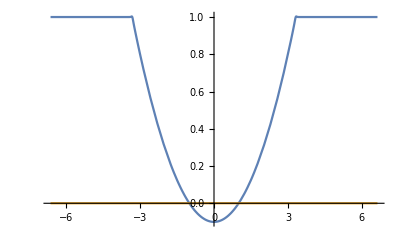

```mathematica
(*Configuration*)
a=0.1;
v=0.0001;
n=100;

b=(1+1/a)^(-n);
Epsilon = Function[x,1+(a*(x^2-1)+ⅈ*v-1)/(1+b*x^(2n))];

X0=2*Sqrt[1/a+1];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

χ=33;
A=1;
t=0.1;
```

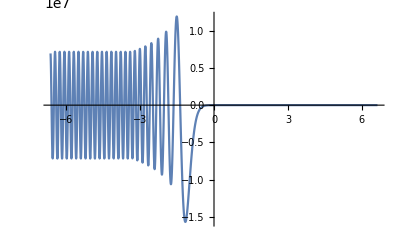

0.0382141

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+χ^2*(Epsilon[x]-Sin[teta]^2)*y[x]==0};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A};

ETE=ParametricNDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0},{teta}];
Plot[Re[ETE[0][x]],{x,-X0,X0},PlotRange->Full]

RTE=Function[teta,Exp[2*ⅈ*χ*(-X0)]*(ⅈ*χ*ETE[teta][-X0]-ETE[teta]'[-X0])/(ⅈ*χ*ETE[teta][-X0]+ETE[teta]'[-X0])];
TTE=Function[teta,ETE[teta][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTE[teta]*Exp[-ⅈ*χ*(-X0)])/ETE[teta][-X0]];

TEDissipation =Function[teta,1 - Abs[RTE[teta]]^2-Abs[TTE[teta]]^2];
(*Plot[TEDissipation[x],{x,-π/2,π/2},PlotRange->Full]*)
TEDissipation[t]
```

NDSolveValue::precw: The precision of the differential equation ({1089 (0.9900332889206208`  + Power[« 2 »] Plus[« 2 »]) y[x] - (0.2` x Power[« 2 »] - 1.4513143180296405`*^-102 Power[« 2 »] Power[« 2 »] Plus[« 2 »]) SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (30.).

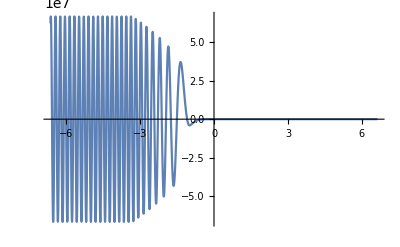

0.447831

```mathematica
(*TM-wave*)
BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2*(Epsilon[x]-Sin[t]^2)*y[x]==0};
BTMInitials={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[t]};

BTM=NDSolveValue[{BTMEquation,BTMInitials},y,{x,-X0,X0},WorkingPrecision->30,MaxSteps->10^6];
Plot[Re[BTM[x]],{x,-X0,X0},PlotRange->Full]

RTM=Exp[2*ⅈ*χ*(-X0)]*(ⅈ*χ*BTM[-X0]-BTM'[-X0])/(ⅈ*χ*BTM[-X0]+BTM'[-X0]);
TTM=BTM[X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTM*Exp[-ⅈ*χ*(-X0)])/BTM[-X0];

TMDissipation=1-Abs[RTM]^2-Abs[TTM]^2
```

InterpolatingFunction::dmval: Input value {-6.63298} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {-6.63298} lies outside the range of data in the interpolating function. Extrapolation will be used.

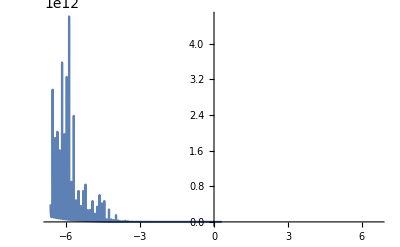

```mathematica
(*Reletive precision*)
ETM=Function[x,Piecewise[{{ⅈ*BTM1'[x]/(χ*Epsilon[x]),x>1+step},{ⅈ*BTM2'[x]/(χ*Epsilon[x]),1-step>x>-1+step},{ⅈ*BTM3'[x]/(χ*Epsilon[x]),x<-1-step}}]];
Plot[Abs[ETE[0][x]-ETM[x]]/Min[Abs[ETE[0][x]],Abs[ETM[x]]],{x,-X0,X0},PlotRange->Full]

BTE=Function[x,(-ⅈ/χ)*ETE[0]'[x]];
Plot[Abs[BTE[x]+BTM[x]]/Min[Abs[BTE[x]],Abs[BTM[x]]],{x,-X0,X0},PlotRange->Full]
```

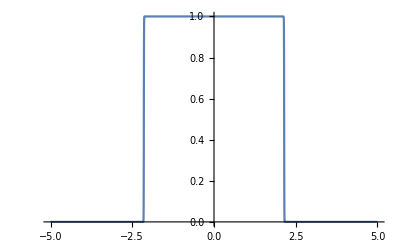

```mathematica
Plot[1/(1+Exp[Exp[x^2]-100]),{x,-5,5}]
```